Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2023/24
F.Javier Muñoz Delgado

# Notas y Prácticas 8: Funciones de varias variables I (Funciones, límites)

## Funciones de varias variables.

## Definir una función de varias variables. Evaluar una función de varias variables Dibujar la gráfica de una función de dos variables (en rectángulos o en otros recintos) Dibujar curvas de nivel de una función de dos variables (ContourPlot) Estudio del límite de una función de dos variables (límites reiterados, direccionales, por conjuntos)

Para definir una función de varias variables el proceso es similar. Basta poner todas las variables de la que dependa la función.

```mathematica
f[x_,y_,z_]:= x Cos[y] + z Sin[x]
```

Una vez definida la función se puede evaluar en uno o varios puntos.

```mathematica
f[1,0,0]
```

1

```mathematica
{f[2,1,0],f[2,-1,0],f[0,0,0]}
```

{2 Cos[1],2 Cos[1],0}

Para dibujar gráficas, nos debemos limitar a funciones de dos variables.

```mathematica
g[x_,y_]:= x^2+ y^2
```

```mathematica
Plot3D[g[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Si queremos dibujar la gráfica en otro conjunto que no sea un rectángulo de lados paralelos a los ejes, podemos utilizar la función Which y restringir el recinto donde dibujamos.

```mathematica
Plot3D[Which[x^2+y^2≤9,g[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

Para mejorar la gráfica podemos pedir al Mathematica que dibuje más puntos.

```mathematica
Plot3D[Which[x^2+y^2≤9,g[x,y]],{x,-3,3},{y,-3,3}, PlotPoints->100]
```

-Graphics3D-

Otra forma de hacernos una idea de cómo se comporta una función es dibujar curvas de nivel.

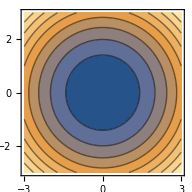

```mathematica
ContourPlot[g[x,y],{x,-3,3},{y,-3,3}]
```

Las curvas de nivel podrían verse como la intersección de la gráfica con planos paralelos a diferentes alturas.

```mathematica
Plot3D[{2,4,6,8,Which[x^2+y^2≤9,g[x,y]]},{x,-3,3},{y,-3,3},PlotPoints->100]
```

-Graphics3D-

En este caso, aparecen dibujadas varias curvas de nivel (el valor se puede ver al pasar el cursor). Todas las curvas de nivel son circunferencias. Líneas más juntas significa que la función varía más rápidamente. Vemos que al alejarnos del (0,0) las curvas de nivel aparecen más juntas, esto significa que la función varía de forma más rápida.

También podemos dibujar sólo una curva de nivel correspondiente a un valor, o varias curvas correspondientes a varios valores.

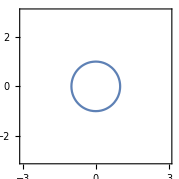

```mathematica
ContourPlot[g[x,y]==1,{x,-3,3},{y,-3,3}]
```

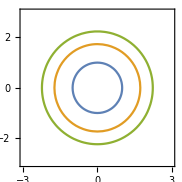

```mathematica
ContourPlot[{g[x,y]==1,g[x,y]==3,g[x,y]==5},{x,-3,3},{y,-3,3}]
```

```mathematica
h[x_,y_]:= Abs[x]+Abs[y]
```

Para dibujar muchas, puede ser más fácil con la función Table.

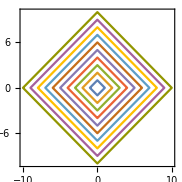

```mathematica
ContourPlot[Evaluate[Table[h[x,y]==i,{i,1,10}]],{x,-10,10},{y,-10,10}]
```

Cálculo de límites.

La mayoría de las funciones con las que trabajamos son continuas (suelen ser múltiplos, sumas, restas, productos, cocientes o composiciones de funciones continuas). En este caso, el valor del límite en cualquier punto del dominio coincide con el valor de la función (hallar el límite es tan simple como evaluar la función en el punto). También podemos preguntarnos por el límite de una función en un punto que no esté en el dominio, aunque sí “junto” al dominio, o por el límite en el infinito (es decir, cuando nos “alejamos” mucho).

```mathematica
k[x_,y_]:= (x y)/(x^2+y^2)
```

Esta función es un cociente de funciones continuas, polinomios, por tanto es continua en todo su dominio. El dominio no es todo el plano, pues el denominador no puede ser cero. Por tanto, el domino es todo el plano menos el (0,0). Podemos preguntarnos por el límite en cualquier punto del plano y en el infinito. En los puntos del dominio, el límite es igual al valor de la función. Estudiemos el caso del punto (0,0).

```mathematica
Plot3D[k[x,y],{x,-3,3},{y,-3,3},PlotPoints->100]
```

-Graphics3D-

La gráfica nos muestra algo “raro” alrededor del punto (0,0) y que seguramente no habrá límite.
Podríamos acercarnos por puntos de la forma (x,0) o por puntos de la forma (0,y). En ambos casos, la función vale cero y este sería el candidato a ser el valor del límite. Sin embargo, si nos acercamos por puntos donde x=y, nos encontramos que la función vale 1/2. La conclusión es que el límite no puede existir, pues al acercarnos por caminos distintos, la función tiende a valores diferentes.
Con el Mathematica, podemos calcular límites direccionales.

```mathematica
Limit[k[x,y]/.y->t x,x->0]
```

t/(1+t^2)

Al acercarnos por puntos de la forma (x, t x), rectas de pendiente t, obtenemos diferentes valores. El límite no existe.

Lo mismo ocurriría si estudiamos el límite en el infinito. Por puntos de la forma (x,0) o (y,0) nos podemos alejar tanto como queramos y la función vale 0. Si nos alejamos por puntos de la forma (x,x) la función vale 1/2. Por tanto, no existe el límite de la función en el infinito.

```mathematica
k[x_,y_]:= (x y^2)/(x^2+y^4)
```

Esta es otra función que es continua en todo su dominio (cociente de continuas) que es todo el plano menos el punto (0,0) (que es el único punto donde se anula el denominador).

```mathematica
Plot3D[k[x,y],{x,-3,3},{y,-3,3},PlotPoints->400]
```

-Graphics3D-

También presenta unos pliegues “extraños” alrededor del punto (0,0) y podemos sospechar que no habrá límite. Calculemos los límites direccionales.

```mathematica
Limit[k[x,y]/.y->t x,x->0]
```

0

Todos los límites direccionales nos llevan al valor cero. A mano, si evaluamos la función en los puntos de la forma (x,tx) nos encontramos que 

	k(x,tx)= (x (tx)^2)/(x^2+(tx)^4)=(x^3 t^2)/(x^2+t^4 x^4)= (x t^2)/(1+t^4 x^2) que tiende a 0 cuando x tiende a 0.
Podríamos pensar que si por todas las direcciones el límite es cero, el límite debe ser cero. Sin embargo, podemos encontrar otros caminos por los cuales la función se acerque a otros valores.

```mathematica
k[y^2,y]
```

1/2

```mathematica
k[x,y]/.x->y^2
```

1/2

```mathematica
Limit[k[x,y]/.x->y^2,y->0]
```

1/2

Vemos que al acercarnos por puntos de la forma (y^2,y) la función vale 1/2. Por tanto, el límite en el (0,0) no existe. 
De manera similar, podemos ver que tampoco existe el límite en infinito (si nos alejamos por los ejes la función vale 0 y si lo hacemos por puntos de la forma (y^2,y) la función vale 1/2). 

Un par de observaciones:
1) ¿Qué ocurre con los límites en otros puntos diferentes al (0,0)?

Por ejemplo, si estudiamos lim_((x,y)→(1,0)) (4(x-1)^2 -3 y^2)/(2(x-1)^2+5 y^2), una posibilidad es cambiar las coordenadas y escribir X=x-1, e Y=y. Así, la expresión queda como (4 X^2 -3 Y^2)/(2X+5 Y^2). Respecto al límite, cuando x→1, tenemos que X=x-1→0. De esta forma podemos escribir el límite como  lim_((X,Y)→(1,0)) (4 X^2 -3 Y^2)/(2X+5 Y^2).  Hemos cambiado el límite en el punto (1,0) en otro en el punto (0,0).

2) ¿Podemos utilizar herramientas para el cálculo de límites de funciones de una variable, en límites de dos variables?

En general, no podemos calcular los límites, dejando fija una variable y haciendo el límite en la otra. Como hemos visto antes en muchos ejemplos, el límite siguiendo una recta (o eje)  puede existir y el límite no.
No obstante, hay ocasiones en que la función puede quedar en términos de una variable. Estudiemos el límite: lim_((x,y)→(0,0)) (1-cos(x^2+y^2))/(x^2+y^2). Si hacemos el cambio a coordenadas polares, la expresión queda como (1-cos(r^2))/r^2. El límite quedaría como lim_(r→0) (1-cos(r^2))/r^2. Como en esta expresión el ángulo, o argumento, no aparece, podríamos utilizar herramientas como la Regla de L’Hôpital. Dado que numerador y denominador tienden a 0, y se cumplen las condiciones de la regla de L’Hôpital, derivamos en numerador y denominador, (sen(r^2)2r)/(2r)= sen(r^2)→ 0. Por tanto, lim_(r→0) (1-cos(r^2))/r^2=0 y  lim_((x,y)→(0,0)) (1-cos(x^2+y^2))/(x^2+y^2)=0

## 8.- Estudiar la continuidad de la función f(x,y)=Piecewise[{{(2xy)/(x^2+y^2), si (x,y)≠(0,0)}, {0, si (x,y)=(0,0)}}] Julio 22

Solución:
La función f(x,y) en los puntos distintos del (0,0) es un cociente de dos polinomios, que son funciones continuas. Por tanto, la función es continua en todos los puntos distintos del (0,0). Faltaría estudiar la continuidad en el punto (0,0). Para que sea continua en ese punto, es necesario que exista el límite y que coincida con el valor de la función en el (0,0), que es 0.

Para estudiar el límite, podemos probar a acercarnos al punto por diversos caminos. 

Si nos acercamos al punto (0,0) por puntos de la forma (x,0) (puntos del eje horizontal) f(x,0) = (2x*0)/(x^2+0)=0.
Si nos acercamos al punto (0,0) por puntos de la forma (x,x) (puntos de la diagonal del primer y tercer cuadrante) f(x,x) = (2xx)/(x^2+x^2)= (2 x^2)/(2 x^2)= 1.
Dado que podemos acercarnos al (0,0) por dos caminos distintos, tomando valores distintos, no existe límite en el punto (0,0). Por tanto, la función no es continua en el punto (0,0). Sí es continua en el resto de puntos del plano.

## 8.- Calcular si existe el límite de la función f(x,y)= (3x-2y)/(x^2+ y^2) en el infinito. Junio 21

Solución:
Podemos pasar a coordenadas polares.

(3x-2y)/(x^2+ y^2)= (3ρ cos θ - 2 ρ sen θ)/ρ^2 = (3 cos θ - 2sen θ)/ρ

Vemos que cuando nos alejamos, es decir, cuando ρ → ∞, la expresión tiende a 0, con independencia de los valores de θ.

El límite de la función en el infinito es cero.

## 6.- Calcular si existe el límite de la función f(x,y)= (x^3+y^3)/(x^2+y^2) en el punto (0,0). Enero 19

Solución.
Al acercarnos al punto (0,0), tanto el numerador como el denominador tienden a cero. Cambiando a coordenadas polares, x=ρ cos θ, y= ρ sen θ, nos queda la expresión  (x^3+y^3)/(x^2+y^2) = ((ρ cos θ)^3+(ρ sen θ)^3)/((ρ cos θ)^2+(ρ sen θ)^2)=(ρ^3((cos θ)^3+(sen θ)^3))/ρ^2=ρ((cos θ)^3+(sen θ)^3)⟶0 , cuando ρ⟶0. Por tanto, el límite existe y es cero.

## 7.- Estudiar, utilizando el cambio a coordenadas polares, el límite de la función f(x,y)= (x^2 y)/(x^2+y^2) en el punto (0,0). Enero 20

Solución.
Hacemos el cambio a coordenadas polares f(x,y)= (x^2 y)/(x^2+y^2)=  (r^2 cos^2 θ r sen θ)/r^2= r cos^2 θ  sen θ ⟶0 (cuando (x,y)⟶(0,0), es decir cuando r ⟶0). El límite existe y vale 0.

## 8.- Calcular si existe el límite de la función f(x,y)= x^2/(2 x^2- 3 y^2) en el punto (0,0).

Solución:
Observamos que cuando x e y están próximos a cero, tanto el numerador como el denominador están próximos a cero. Tendríamos una indeterminación.
Vamos a acercarnos al punto (0,0) desde diferentes direcciones. 
1) Por puntos de la forma (x,0), la función vale f(x,0)= x^2/(2 x^2) = 1/2 
2) Por puntos de la forma (0,y), la función vale f(0,y)= 0/(-3 y^2)=0 
Dado que podemos aproximarnos al (0,0) por dos caminos distintos, tomando valores diferentes, concluimos que no existe el límite.

## 8.- Calcular si existe el límite de la función f(x,y)= x^2/(x^2+y^2) en el punto (0,0). Enero 18

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida. Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/y^2=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma x=y, f(x,x)= x^2/(x^2+x^2) = 1/2. Por tanto, el limite por esta dirección sería 1/2.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto 0.

## 7.- Calcular si existe el límite de la función f(x,y)= x/(x+2y) en el punto (0,0). Enero 19

Solución:
La función f es un cociente de dos polinomios, por tanto es continua en todos los puntos donde está definida.
 Por ello, el límite en todos los puntos donde está definida es el valor de la función. El problema es que en el punto (0,0) el denominador se anula y la función no está definida en ese punto. Al acercarnos al punto (0,0) tanto el numerador como el denominador se acercan a 0, sería una indeterminación y habría que hacer cálculos para ver si hay o no límite y cuánto valdría.

Probamos a acercarnos al (0,0) por diferentes caminos:

1) Nos acercamos por puntos de la forma x=0, f(0,y)= 0/(2y)=0. Por tanto, el limite por esta dirección sería 0.
2) Nos acercamos por puntos de la forma y=0, f(x,0)= x/(x+2*0) = 1 . Por tanto, el limite por esta dirección sería 1.
Como hemos encontrado dos direcciones con límites diferentes, concluimos que no existe el límite en el punto (0,0).